## Fixed purity

Eigenvalues

## Normalisation factors

Eq 30

```mathematica
Sum[((1+r)/2)^l((1-r)/2)^(n-l)1/(2s+1),{l,n/2-s,n/2+s}]//FullSimplify
```

(2^(-1-n) (1-r^2)^(1/2 (n-2 s)) (-(1-r)^(1+2 s)+(1+r)^(1+2 s)))/(r+2 r s)

```mathematica
f[s_,n_,r_]:=(((1-r^2)/4)^(1/2 (n-2 s)) (-((1-r)/2)^(1+2 s)+((1+r)/2)^(1+2 s)))/(r(2s+1))
```

## Eigenvalues and signs

### Normalisation

Eq 44

```mathematica
R1[s_,n_,r1_]=f[s+1/2,n+1,r1]/f[s,n,r1]
```

(2^(-1-2 s+2 (1/2+s)) (1-r1^2)^(1/2 (-n+2 s)+1/2 (1+n-2 (1/2+s))) (-2^(-1-2 (1/2+s)) (1-r1)^(1+2 (1/2+s))+2^(-1-2 (1/2+s)) (1+r1)^(1+2 (1/2+s))) (1+2 s))/((-2^(-1-2 s) (1-r1)^(1+2 s)+2^(-1-2 s) (1+r1)^(1+2 s)) (1+2 (1/2+s)))

```mathematica
f[s+1/2,n+1,r1]/f[s,n,r1]//FullSimplify
```

((-(1-r1)^(2 (1+s))+(1+r1)^(2+2 s)) (1+2 s))/(4 (-(1-r1)^(1+2 s)+(1+r1)^(1+2 s)) (1+s))

```mathematica
R2[s_,n_,r1_]=f[s-1/2,n+1,r1]/f[s,n,r1]
```

(2^(-1+2 (-1/2+s)-2 s) (1-r1^2)^(1/2 (1+n-2 (-1/2+s))+1/2 (-n+2 s)) (-2^(-1-2 (-1/2+s)) (1-r1)^(1+2 (-1/2+s))+2^(-1-2 (-1/2+s)) (1+r1)^(1+2 (-1/2+s))) (1+2 s))/((-2^(-1-2 s) (1-r1)^(1+2 s)+2^(-1-2 s) (1+r1)^(1+2 s)) (1+2 (-1/2+s)))

```mathematica
f[s-1/2,n+1,r1]/f[s,n,r1]//FullSimplify
```

((-1+r1^2) ((1-r1)^(2 s)-(1+r1)^(2 s)) (1+2 s))/(4 (-(1-r1)^(1+2 s)+(1+r1)^(1+2 s)) s)

In the asymptotic limit s~n and terms with 1-r1 can be neglected, as exponentially suppressed. At this level of approximation R1 and R2 are

```mathematica
fn1[s_,n_,r1_]:=((1+r1) (1+2 s))/(4 (1+s))
```

```mathematica
fn2[s_,n_,r1_]:=-((-1+r1) (1+2 s))/(4 s)
```

### 1x1 case

#### case a)

Exact Eigenvalue

```mathematica
λ1[s_,t_,n_,r1_,r2_]:=f[s+1/2,n+1,r1]f[t,n,r2]-f[s,n,r1]f[t+1/2,n+1,r2]
```

Approximated normalised eigenvalue

```mathematica
λ1n[s_,t_,n_,r1_,r2_]:=fn1[s,n,r1]-fn1[t,n,r2]
```

```mathematica
λ1n[s,t,n,r1,r2]//FullSimplify
```

1/4 (((1+r1) (1+2 s))/(1+s)-((1+r2) (1+2 t))/(1+t))

Expanding around s~n r1, t ~n r2 we have

```mathematica
Series[λ1n[s,t,n,r1,r2],{s, n *r1,2 },{t,n *r2,2}]
```

((((1+r1) (1+2 n r1))/(4 (1+n r1))-((1+r2) (1+2 n r2))/(4 (1+n r2)))+((-1-r2) (t-n r2))/(4 (1+n r2)^2)+((1+r2) (t-n r2)^2)/(4 (1+n r2)^3)+O[t-n r2]^3)+((1+r1) (s-n r1))/(4 (1+n r1)^2)+((-1-r1) (s-n r1)^2)/(4 (1+n r1)^3)+O[s-n r1]^3

```mathematica
Limit[Series[λ1n[s,t,n,r1,r2],{s, n *r1,2 },{t,n *r2,2}],n->Infinity]//FullSimplify
```

(r1-r2)/2

-> positive sign if r1>r2, negative if r1<r2

#### case b)

Exact Eigenvalue

```mathematica
λ2[s_,t_,n_,r1_,r2_]:=f[s+1/2,n+1,r1]f[t,n,r2]-f[s,n,r1]f[t-1/2,n+1,r2]
```

Approximated normalised eigenvalue

```mathematica
λ2n[s_,t_,n_,r1_,r2_]:=fn1[s,n,r1]-fn2[t,n,r2]
```

Expanding around s~n r1, t ~n r2 we have

```mathematica
Limit[Series[λ2n[s,t,n,r1,r2],{s, n *r1,2 },{t,n *r2,2}],n->Infinity]//FullSimplify
```

(r1+r2)/2

-> postitive sign

#### case c)

Exact Eigenvalue

```mathematica
λ3[s_,t_,n_,r1_,r2_]:=f[s-1/2,n+1,r1]f[t,n,r2]-f[s,n,r1]f[t+1/2,n+1,r2]
```

Approximated normalised eigenvalue

```mathematica
λ3n[s_,t_,n_,r1_,r2_]:=fn2[s,n,r1]-fn1[t,n,r2]
```

Expanding around s~n r1, t ~n r2 we have

```mathematica
Limit[Series[λ3n[s,t,n,r1,r2],{s, n *r1,2 },{t,n *r2,2}],n->Infinity]//FullSimplify
```

1/2 (-r1-r2)

-> negative sign

#### 2x2 case

Wigner 6j squared

```mathematica
SixJSymbol[{s+1/2,s,1/2},{t+1/2,t,q}]
```

Piecewise[{{-((ⅈ (-1)^(-q-s-t) √((2 s)!) √((1/2+q+s-t)!) √((2 t)!) √((1/2+q-s+t)!))/(√((2+2 s)!) √((-1/2+q+s-t)!) √((-1/2+q-s+t)!) √((2+2 t)!))), 1/2+2 s≥1/2&&s≥0&&s≥0&&((t==0&&s≥-1/2&&q==1/2 (1+2 s))||(t>0&&s≥1/2 (-1+2 t)&&1/2 (1+2 s-2 t)≤q≤1/2 (1+2 s+2 t))||(s==-1/2&&t>0&&q==t)||(t>0&&-1/2<s<1/2 (-1+2 t)&&1/2 (-1-2 s+2 t)≤q≤1/2 (1+2 s+2 t)))&&((q==0&&Re[t]≥0&&Im[t]==0&&s==1/2 (-1+2 t))||(s>-1/2&&0<q≤1/2 (1+2 s)&&1/2 (1-2 q+2 s)≤t≤1/2 (1+2 q+2 s))||(s==-1/2&&Re[t]>0&&Im[t]==0&&q==t)||(s>-1/2&&q>1/2 (1+2 s)&&1/2 (-1+2 q-2 s)≤t≤1/2 (1+2 q+2 s)))&&((q==0&&t≥0&&s==1/2 (-1+2 t))||(t>0&&0<q≤t&&1/2 (-1-2 q+2 t)≤s≤1/2 (-1+2 q+2 t))||(t==0&&Re[s]>-1/2&&Im[s]==0&&q==1/2 (1+2 s))||(t>0&&q>t&&1/2 (-1+2 q-2 t)≤s≤1/2 (-1+2 q+2 t)))&&((s==0&&t≥-1/2&&q==1/2 (1+2 t))||(t>-1/2&&0<s≤1/2 (1+2 t)&&1/2 (1-2 s+2 t)≤q≤1/2 (1+2 s+2 t))||(t==-1/2&&s>0&&q==s)||(t>-1/2&&s>1/2 (1+2 t)&&1/2 (-1+2 s-2 t)≤q≤1/2 (1+2 s+2 t)))&&((q==0&&t≥-1/2&&s==1/2 (1+2 t))||(t>-1/2&&0<q≤1/2 (1+2 t)&&1/2 (1-2 q+2 t)≤s≤1/2 (1+2 q+2 t))||(t==-1/2&&Re[s]>0&&Im[s]==0&&q==s)||(t>-1/2&&q>1/2 (1+2 t)&&1/2 (-1+2 q-2 t)≤s≤1/2 (1+2 q+2 t)))&&((q==0&&Re[t]≥-1/2&&Im[t]==0&&s==1/2 (1+2 t))||(s>0&&0<q≤s&&1/2 (-1-2 q+2 s)≤t≤1/2 (-1+2 q+2 s))||(s==0&&Re[t]>-1/2&&Im[t]==0&&q==1/2 (1+2 t))||(s>0&&q>s&&1/2 (-1+2 q-2 s)≤t≤1/2 (-1+2 q+2 s)))&&1/2+2 t≥1/2&&t≥0&&t≥0}, {0, True}}]

C++ coefficient squared is then

```mathematica
W[s_,t_,q_]:=((1/2+q-s+t)(1/2+q+s-t))/((2s+1)(2t+1))
```

Exact eigenvalues 2x2:

```mathematica
g[s_,t_,n_,r1_,r2_]:=f[s+1/2,n+1,r1]f[t,n,r2]-f[s-1/2,n+1,r1]f[t,n,r2]
```

```mathematica
a[s_,t_,n_,r1_,r2_]:=1/2(f[s+1/2,n+1,r1]f[t,n,r2]+f[s-1/2,n+1,r1]f[t,n,r2]-f[s,n,r1]f[t+1/2,n+1,r2]-f[s,n,r1]f[t-1/2,n+1,r2])
```

```mathematica
bc[s_,t_,q_,n_,r1_,r2_]:=1/4(g[s,t,n,r1,r2]+g[t,s,n,r2,r1])^2-g[s,t,n,r1,r2]g[t,s,n,r2,r1]W[s,t,q]
```

```mathematica
Eigen1[s_,t_,q_,n_,r1_,r2_]:=a[s,t,n,r1,r2]+Sqrt[bc[s,t,q,n,r1,r2]]
```

```mathematica
Eigen2[s_,t_,q_,n_,r1_,r2_]:=a[s,t,n,r1,r2]-Sqrt[bc[s,t,q,n,r1,r2]]
```

Approximated and normalised:

```mathematica
gn[s_,t_,n_,r1_,r2_]:=fn1[s,n,r1]-fn2[s,n,r1]
```

```mathematica
an[s_,t_,n_,r1_,r2_]:=1/2(fn1[s,n,r1]+fn2[s,n,r1]-fn1[t,n,r2]-fn2 [t,n,r2])
```

```mathematica
bcn[s_,t_,q_,n_,r1_,r2_]:=1/4(gn[s,t,n,r1,r2]+gn[t,s,n,r2,r1])^2-gn[s,t,n,r1,r2]gn[t,s,n,r2,r1]W[s,t,q]
```

```mathematica
Eigen1n[s_,t_,q_,n_,r1_,r2_]:=an[s,t,n,r1,r2]+Sqrt[bcn[s,t,q,n,r1,r2]]
```

```mathematica
Eigen2n[s_,t_,q_,n_,r1_,r2_]:=an[s,t,n,r1,r2]-Sqrt[bcn[s,t,q,n,r1,r2]]
```

```mathematica
Series[Eigen1n[s,t,q,n,r1,r2]/.q->s+t-1/2 /.t->n r2/2 /.s->n r1/2 ,{n,Infinity,1}]
```

1/2 √((r1-r2)^2)+(-1+r1+r1/(2 r2)+r2+r2/(2 r1))/(√(r1^2-2 r1 r2+r2^2) n)+O[1/n]^2

```mathematica
Plot3D[-1+r1+r1/(2 r2)+r2+r2/(2 r1),{r1,0,1},{r2,0,1}]
```

-Graphics3D-

-> postitive sign

```mathematica
Limit[Eigen2n[s,t,q,n,r1,r2]/.q->s+t-1/2 /.t->n r2/2 /.s->n r1/2 ,n->Infinity]
```

-1/2 √((r1-r2)^2)

```mathematica
Series[Eigen2n[s,t,q,n,r1,r2]/.q->s+t-1/2 /.t->n r2/2 /.s->n r1/2 ,{n,Infinity,1}]
```

-1/2 √((r1-r2)^2)-(-1+r1+r1/(2 r2)+r2+r2/(2 r1))/(√(r1^2-2 r1 r2+r2^2) n)+O[1/n]^2

-> negative sign

Asymptotic error probability

### Perr

multiplicity of the irreps

```mathematica
mult[s_,n_]:= (n!)/(((n-2s)/2)!((n+2s)/2+1)!)(2s+1)
```

In general the error probability is (for n even)

```mathematica
Perr[n_,r1_,r2_]:=1/2(1-(Sum[mult[s,n]mult[t,n]((2(t+s+1/2)+1)Abs[λ1[s,t,n,r1,r2]]+(2(t-s-1/2)+1)Abs[λ2[s,t,n,r1,r2]]+Sum[(2q+1)(Abs[Eigen1[s,t,q,n,r1,r2]]+Abs[Eigen2[s,t,q,n,r1,r2]]),{q,t-s+1/2,s+t-1/2}]),{s,0, n/2},{t,s+1,n/2}]+
Sum[mult[s,n]mult[t,n]((2(t+s+1/2)+1)Abs[λ1[s,t,n,r1,r2]]+(2(-t+s-1/2)+1)Abs[λ3[s,t,n,r1,r2]]+Sum[(2q+1)(Abs[Eigen1[s,t,q,n,r1,r2]]+Abs[Eigen2[s,t,q,n,r1,r2]]),{q,s-t+1/2,s+t-1/2}]),{t,0, n/2},{s,t+1,n/2}]+
Sum[mult[t,n]mult[t,n]((2(2t+1/2)+1)Abs[λ1[t,t,n,r1,r2]]+Sum[(2q+1)(Abs[Eigen1[t,t,q,n,r1,r2]]+Abs[Eigen2[t,t,q,n,r1,r2]]),{q,1/2,2t-1/2}]),{t,0, n/2}])/2)
```

with the results of the previous section we can instead calculate the contributions of λ1, λ3 and Eigen1

## Normalisation factors

Corrections to the binomial distribution

```mathematica
(f[s,n,r]mult[s,n])/(Binomial[n,n/2+ s]((1+r)/2)^(n/2+ s)((1-r)/2)^(n/2- s))//FullSimplify
```

((1+r)^(-2 s) (-(1-r)^(1+2 s)+(1+r)^(1+2 s)))/(r (2+n+2 s))

Neglecting (1-r) terms

```mathematica
((1+r)^(-2 s) (+(1+r)^(1+2 s)))/(r (2+n+2 s))//FullSimplify
```

(1+r)/(r (2+n+2 s))

Expansion around the mean

```mathematica
Do[normfact1[a]=SeriesCoefficient[(1+r1)/(r1 (2+n+2 s)),{s,n*r1/2,a}],{a,0,3}]
```

```mathematica
Do[normfact2[a]=SeriesCoefficient[(1+r2)/(r2 (2+n+2 t)),{t,n*r2/2,a}],{a,0,3}]
```

## λ1

```mathematica
Do[λ1coff[a,b]=SeriesCoefficient[(2(t+s+1/2)+1)λ1n[s,t,n,r1,r2],{s,n*r1/2,a},{t,n*r2/2,b}],{a,0,3},{b,0,3-a}]
```

Check asymptotics 
Series[λ1coff[0,0],{n,Infinity,0}]
1/2 (r1^2-r2^2) n+(r1+r1/(2 r2)-r2-r2/(2 r1))+O[1/n]^1
Series[λ1coff[1,0],{n,Infinity,0}]
(r1-r2)+O[1/n]^1
Series[λ1coff[0,1],{n,Infinity,0}]
(r1-r2)+O[1/n]^1
Series[λ1coff[1,1],{n,Infinity,0}]
O[1/n]^2
Series[λ1coff[2,0],{n,Infinity,0}]
O[1/n]^2
Series[λ1coff[0,2],{n,Infinity,0}]
O[1/n]^2

asymptotic expansion at 2nd order

```mathematica
λ1piece=λ1coff[0,0]normfact1[0]normfact2[0]+n (1-r1^2)/4(λ1coff[2,0]normfact1[0]normfact2[0]+λ1coff[1,0]normfact1[1]normfact2[0]+λ1coff[0,0]normfact1[2]normfact2[0])+n (1-r2^2)/4(λ1coff[0,2]normfact1[0]normfact2[0]+λ1coff[0,1]normfact1[0]normfact2[1]+λ1coff[0,0]normfact1[0]normfact2[2]);
```

```mathematica
Series[λ1piece,{n,Infinity,1}]
```

(r1/(2 r2)-r2/(2 r1))/n+O[1/n]^2

## λ2

```mathematica
λ2n[s,t,n,r1,r2]
```

((1+r1) (1+2 s))/(4 (1+s))+((-1+r2) (1+2 t))/(4 t)

```mathematica
Do[λ2coff[a,b]=SeriesCoefficient[(2(t-s-1/2)+1)λ2n[s,t,n,r1,r2],{s,n*r1/2,a},{t,n*r2/2,b}],{a,0,3},{b,0,3-a}]
```

Check asymptotics

```mathematica
Series[λ2coff[0,0],{n,Infinity,0}]
```

1/2 (-r1^2+r2^2) n+(r1/(2 r2)-r2/(2 r1))+O[1/n]^1

```mathematica
Series[λ2coff[1,0],{n,Infinity,0}]

Series[λ2coff[0,1],{n,Infinity,0}]

Series[λ2coff[1,1],{n,Infinity,0}]

Series[λ2coff[2,0],{n,Infinity,0}]

Series[λ2coff[0,2],{n,Infinity,0}]
```

(-r1-r2)+O[1/n]^1

(r1+r2)+O[1/n]^1

O[1/n]^2

O[1/n]^2

O[1/n]^2

asymptotic expansion at 2nd order

```mathematica
λ2piece=λ2coff[0,0]normfact1[0]normfact2[0]+n (1-r1^2)/4(λ2coff[2,0]normfact1[0]normfact2[0]+λ2coff[1,0]normfact1[1]normfact2[0]+λ2coff[0,0]normfact1[2]normfact2[0])+n (1-r2^2)/4(λ2coff[0,2]normfact1[0]normfact2[0]+λ2coff[0,1]normfact1[0]normfact2[1]+λ2coff[0,0]normfact1[0]normfact2[2]);
```

```mathematica
Series[λ2piece,{n,Infinity,1}]
```

(-r1/(2 r2)+r2/(2 r1))/n+O[1/n]^2

## λ3

```mathematica
Do[λ3coff[a,b]=SeriesCoefficient[(2(s-t-1/2)+1)λ3n[s,t,n,r1,r2],{s,n*r1/2,a},{t,n*r2/2,b}],{a,0,3},{b,0,3-a}]
```

Check asymptotics

```mathematica
Series[λ3coff[0,0],{n,Infinity,0}]
```

1/2 (-r1^2+r2^2) n+(r1/(2 r2)-r2/(2 r1))+O[1/n]^1

```mathematica
Series[λ3coff[1,0],{n,Infinity,0}]

Series[λ3coff[0,1],{n,Infinity,0}]

Series[λ3coff[1,1],{n,Infinity,0}]

Series[λ3coff[2,0],{n,Infinity,0}]

Series[λ3coff[0,2],{n,Infinity,0}]
```

(-r1-r2)+O[1/n]^1

(r1+r2)+O[1/n]^1

O[1/n]^2

O[1/n]^2

O[1/n]^2

asymptotic expansion at 2nd order

```mathematica
λ3piece=λ3coff[0,0]normfact1[0]normfact2[0]+n (1-r1^2)/4(λ3coff[2,0]normfact1[0]normfact2[0]+λ3coff[1,0]normfact1[1]normfact2[0]+λ3coff[0,0]normfact1[2]normfact2[0])+n (1-r2^2)/4(λ3coff[0,2]normfact1[0]normfact2[0]+λ3coff[0,1]normfact1[0]normfact2[1]+λ3coff[0,0]normfact1[0]normfact2[2]);
```

```mathematica
Series[λ3piece,{n,Infinity,1}]
```

(-r1/(2 r2)+r2/(2 r1))/n+O[1/n]^2

## Eigen1

### Contribution a

```mathematica
Sum[2q+1,{q,s-t+1/2,s+t-1/2}]
```

2 (1+2 s) t

```mathematica
an[s,t,n,r1,r2]
```

1/2 (-((-1+r1) (1+2 s))/(4 s)+((1+r1) (1+2 s))/(4 (1+s))+((-1+r2) (1+2 t))/(4 t)-((1+r2) (1+2 t))/(4 (1+t)))

```mathematica
Do[ca[a,b]=SeriesCoefficient[2 (1+2 s) t*an[s,t,n,r1,r2],{s,n*r1/2,a},{t,n*r2/2,b}],{a,0,3},{b,0,3-a}]
```

Check asymptotics

```mathematica
Series[ca[0,0],{n,Infinity,1}]
```

(-r1/2-r1/(2 r2)+r2/2+r2/(2 r1))+(-1/2+r1/r2^2-1/(2 r2)+r1/r2-r2/(2 r1^2)-r2/(2 r1))/n+O[1/n]^2

```mathematica
Series[ca[1,0],{n,Infinity,0}]

Series[ca[0,1],{n,Infinity,0}]

Series[ca[1,1],{n,Infinity,0}]

Series[ca[2,0],{n,Infinity,0}]

Series[ca[0,2],{n,Infinity,0}]
```

r2+O[1/n]^1

-r1+O[1/n]^1

O[1/n]^2

O[1/n]^2

O[1/n]^2

asymptotic expansion at 2nd order

```mathematica
capiece=ca[0,0]normfact1[0]normfact2[0]+n (1-r1^2)/4(ca[2,0]normfact1[0]normfact2[0]+ca[1,0]normfact1[1]normfact2[0]+ca[0,0]normfact1[2]normfact2[0])+n (1-r2^2)/4(ca[0,2]normfact1[0]normfact2[0]+ca[0,1]normfact1[0]normfact2[1]+ca[0,0]normfact1[0]normfact2[2]);
```

### Contribution b

#### MacLaurin approximation of the sum in q

```mathematica
int1=Simplify[Integrate[(2q+1)Sqrt[bcn[s,t,q,n,r1,r2]],q]/.q->s+t-1/2];
```

```mathematica
int2=-Simplify[Integrate[(2q+1)Sqrt[bcn[s,t,q,n,r1,r2]],q]/.q->(s-t)+1/2];
```

```mathematica
extr1=Simplify[(2q+1)Sqrt[bcn[s,t,q,n,r1,r2]]/.q->s+t-1/2];
```

```mathematica
extr2=Simplify[(2q+1)Sqrt[bcn[s,t,q,n,r1,r2]]/.q->(s-t)+1/2];
```

#### Expansion around the mean

Extremes of the integrals

```mathematica
cbextr[0,0]=Series[(extr1+extr2)/2/.{s->n*r1/2,t->n*r2/2},{n,Infinity,-1}]
```

1/2 (1/2 √((r1-r2)^2) (r1+r2)+1/2 (r1-r2) √((r1+r2)^2)) n+O[1/n]^0

```mathematica
cbextr[1,0]=Series[D[(extr1+extr2)/2,{s,1},{t,0}]/.{s->n*r1/2,t->n*r2/2},{n,Infinity,-1}]
```

O[1/n]^0

```mathematica
cbextr[0,1]=Series[D[(extr1+extr2)/2,{s,1},{t,0}]/.{s->n*r1/2,t->n*r2/2},{n,Infinity,-1}]
```

O[1/n]^0

Integral

```mathematica
cb[0,0]=int1+int2/.{s->n*r1/2,t->n*r2/2};
```

```mathematica
cb[1,0]=D[int1+int2,{s,1},{t,0}]/.{s->n*r1/2,t->n*r2/2};
```

```mathematica
cb[0,1]=D[int1+int2,{s,0},{t,1}]/.{s->n*r1/2,t->n*r2/2};
```

```mathematica
cb[1,1]=D[int1+int2,{s,1},{t,1}]/.{s->n*r1/2,t->n*r2/2};
```

```mathematica
cb[2,0]=1/2 D[int1+int2,{s,2},{t,0}]/.{s->n*r1/2,t->n*r2/2};
```

```mathematica
cb[0,2]=1/2 D[int1+int2,{s,0},{t,2}]/.{s->n*r1/2,t->n*r2/2};
```

Check asymptotics

```mathematica
Series[cb[0,0],{n,Infinity,0}]
```

(-1/12 ((r1-r2)^2)^(3/2)+1/12 ((r1+r2)^2)^(3/2)) n^2+(1/3 r1 r2 (-(3 √((r1+r2)^2) (r1^2+2 r1 r2+2 r1^2 r2+r2^2-2 r1 r2^2))/(4 r1^2 r2^2)+((r1+r2)^2)^(3/2) (((1/r2^4-1/r2^3) r2)/(4 r1)+(1/(2 r1)+1/2 (1/r1^2+1/2 (1/r1^4-1/r1^3) r1) r2)/r2^2))+1/3 r1 r2 (-(3 √((r1-r2)^2) (r1^2-2 r1 r2+2 r1^2 r2+r2^2+2 r1 r2^2))/(4 r1^2 r2^2)-(r1^2-2 r1 r2+r2^2)^(3/2) (((1/r2^4-1/r2^3) r2)/(4 r1)+(1/(2 r1)+1/2 (1/r1^2+1/2 (1/r1^4-1/r1^3) r1) r2)/r2^2))) n+((-r1^8+r1^7 r2+2 r1^6 r2^2-r1^7 r2^2+r1^8 r2^2-r1^5 r2^3-3 r1^6 r2^3-2 r1^7 r2^3-2 r1^4 r2^4+4 r1^5 r2^4-13 r1^6 r2^4-r1^3 r2^5+4 r1^4 r2^5+4 r1^5 r2^5+2 r1^2 r2^6-3 r1^3 r2^6-13 r1^4 r2^6+r1 r2^7-r1^2 r2^7-2 r1^3 r2^7-r2^8+r1^2 r2^8)/(12 r1^4 √((r1-r2)^2) r2^4)+1/(12 r1^4 r2^4 (r1+r2)^2)(r1^8 √((r1+r2)^2)+r1^7 r2 √((r1+r2)^2)-2 r1^6 r2^2 √((r1+r2)^2)+r1^7 r2^2 √((r1+r2)^2)-r1^8 r2^2 √((r1+r2)^2)-r1^5 r2^3 √((r1+r2)^2)+5 r1^6 r2^3 √((r1+r2)^2)+2 r1^4 r2^4 √((r1+r2)^2)-2 r1^5 r2^4 √((r1+r2)^2)+9 r1^6 r2^4 √((r1+r2)^2)-r1^3 r2^5 √((r1+r2)^2)-14 r1^4 r2^5 √((r1+r2)^2)-8 r1^5 r2^5 √((r1+r2)^2)-2 r1^2 r2^6 √((r1+r2)^2)-7 r1^3 r2^6 √((r1+r2)^2)+9 r1^4 r2^6 √((r1+r2)^2)+r1 r2^7 √((r1+r2)^2)+r1^2 r2^7 √((r1+r2)^2)+r2^8 √((r1+r2)^2)-r1^2 r2^8 √((r1+r2)^2)))+O[1/n]^1

```mathematica
Series[cb[1,0],{n,Infinity,0}]

Series[cb[0,1],{n,Infinity,0}]
Series[cb[1,1],{n,Infinity,0}]
Series[cb[2,0],{n,Infinity,0}]

Series[cb[0,2],{n,Infinity,0}]
```

(-(((r1-r2)^2)^(3/2))/(6 r1)+(((r1+r2)^2)^(3/2))/(6 r1)) n+1/(6 r1 r2^2)(-r1^2 √((r1-r2)^2)-r1 √((r1-r2)^2) r2-r1^2 √((r1-r2)^2) r2+2 √((r1-r2)^2) r2^2-4 r1 √((r1-r2)^2) r2^2-√((r1-r2)^2) r2^3+r1^2 √((r1+r2)^2)-r1 r2 √((r1+r2)^2)+r1^2 r2 √((r1+r2)^2)-2 r2^2 √((r1+r2)^2)-4 r1 r2^2 √((r1+r2)^2)+r2^3 √((r1+r2)^2))+O[1/n]^1

(-(((-r1+r2)^2)^(3/2))/(6 r2)+(((r1+r2)^2)^(3/2))/(6 r2)) n+1/(6 r1^2 r2)(2 r1^2 √((-r1+r2)^2)-r1^3 √((-r1+r2)^2)-r1 r2 √((-r1+r2)^2)-4 r1^2 r2 √((-r1+r2)^2)-r2^2 √((-r1+r2)^2)-r1 r2^2 √((-r1+r2)^2)-2 r1^2 √((r1+r2)^2)+r1^3 √((r1+r2)^2)-r1 r2 √((r1+r2)^2)+8 r1^2 r2 √((r1+r2)^2)+r2^2 √((r1+r2)^2)+r1 r2^2 √((r1+r2)^2))+O[1/n]^1

(-(((r1-r2)^2)^(3/2))/(3 r1 r2)+(√((r1+r2)^2) (r1^2+2 r1 r2+r2^2))/(3 r1 r2))+O[1/n]^1

O[1/n]^2

O[1/n]^2

asymptotic expansion at 2nd order

```mathematica
cbpiece=cbextr[0,0]normfact1[0]normfact2[0]+cb[0,0]normfact1[0]normfact2[0]+n (1-r1^2)/4(cb[2,0]normfact1[0]normfact2[0]+cb[1,0]normfact1[1]normfact2[0]+cb[0,0]normfact1[2]normfact2[0])+n (1-r2^2)/4(cb[0,2]normfact1[0]normfact2[0]+cb[0,1]normfact1[0]normfact2[1]+cb[0,0]normfact1[0]normfact2[2]);
```

## Final result

Expansion in moments around the mean of the binomial distributions. One can see the relevant terms from the fields named as “check asymptotics”

```mathematica
FullSimplify[1/2(1-Series[cbpiece+capiece+λ1piece, {n,Infinity,1}]),Assumptions->0<r2<r1<1]
```

1/12 (6-3 r1-r2^2/r1)-(-5 r1^2+r2^2)/(12 r1^3 n)+O[1/n]^2

Check generalisation when r2>r1

```mathematica
Series[FullSimplify[1/12 (6-(-((r1-r2)^2)^(3/2)+(r1+r2)^3)/(2 r1 r2))+1/(2n)(1/(12 r1^3 r2^3)(((r1-r2)^2)^(5/2)-((r1+r2)^2)^(5/2)+5r1 r2(((r1+r2)^2)^(3/2)+((r1-r2)^2)^(3/2)))),Assumptions->0<r1<1&&0<r2<1 &&r2<r1],{n,Infinity,1}]
```

(1/2-r1/4-r2^2/(12 r1))+(5/(12 r1)-r2^2/(12 r1^3))/n+O[1/n]^2

```mathematica
Series[FullSimplify[1/12 (6-(-((r1-r2)^2)^(3/2)+(r1+r2)^3)/(2 r1 r2))+1/(2n)(1/(12 r1^3 r2^3)(((r1-r2)^2)^(5/2)-((r1+r2)^2)^(5/2)+5r1 r2(((r1+r2)^2)^(3/2)+((r1-r2)^2)^(3/2)))),Assumptions->0<r1<1&&0<r2<1 &&r1<r2],{n,Infinity,1}]
```

(1/2-r1^2/(12 r2)-r2/4)+(-r1^2/(12 r2^3)+5/(12 r2))/n+O[1/n]^2

```mathematica
Perrasy[n_,r1_,r2_]:=(1/2-r1/4-r2^2/(12 r1))+(5/(12 r1)-r2^2/(12 r1^3))/n
```

Check case r1=r2

```mathematica
((3 r1^2+r2^2)/(6 r1)+(-5 r1^2+r2^2)/(6 r1^3 n)+O[1/n]^2)/.{r2->r1}//Simplify
```

(2 r1)/3-2/(3 r1 n)+O[1/n]^2

#### Plot

Plot for r1=3/4, r2 =1/2

```mathematica
Perrexactlist=Table[{n,Perr[n,3/4,1/2]},{n,10,80,10}]//N
```

$Aborted

```mathematica
Perrexactlist={{10.,0.32744656632483526},{20.,0.3083776080027055},{30.,0.30097243713206806},{40.,0.29706287592034786},{50.,0.29465843457973157},{60.,0.29303433751932784},{70.,0.29186509050473763},{80.,0.29098356467241493}}
```

{{10.,0.327447},{20.,0.308378},{30.,0.300972},{40.,0.297063},{50.,0.294658},{60.,0.293034},{70.,0.291865},{80.,0.290984}}

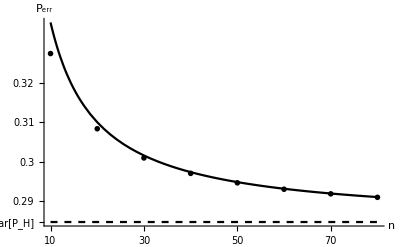

```mathematica
fixpur=Show[ListPlot[Perrexactlist,PlotTheme->"Monochrome"],Plot[1/12 (6-3 r1-r2^2/r1)-(-5 r1^2+r2^2)/(12 r1^3 n)/.{r1->3/4,r2->1/2},{n,10,80},PlotTheme->"Monochrome"],Plot[1/12 (6-3 r1-r2^2/r1)/.{r1->3/4,r2->1/2},{n,10,80},PlotTheme->"Monochrome",PlotStyle->Dashed],AxesLabel->{Style["n",Medium],Style["P_err",Medium]},Ticks->{{10,20,30,40,50,60,70,80},{0.28,{1/12 (6-3 r1-r2^2/r1)/.{r1->3/4,r2->1/2},OverBar["P_H"]},0.29,0.30,0.31,0.32}},AxesOrigin->{10,0.28},PlotRange->All]
```

```mathematica
Export["/Users/Strangeloop/Desktop/learningarticle/revision1/fixpur.eps",fixpur]
```

/Users/Strangeloop/Desktop/learningarticle/revision1/fixpur.eps